```mathematica
c
```

```mathematica
transform1 = {x->r Cos[θ], y->r Sin[θ]};
d=x^2+y^2<4;
range1 = {r, 0, 3};
range2 = {θ, 0, 2 π};
range3 = {x, -3, 3};
range4 = {y, -3, 3};
```

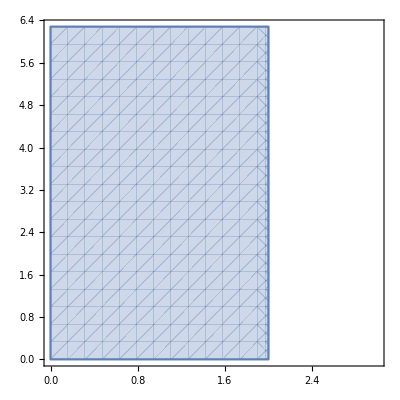

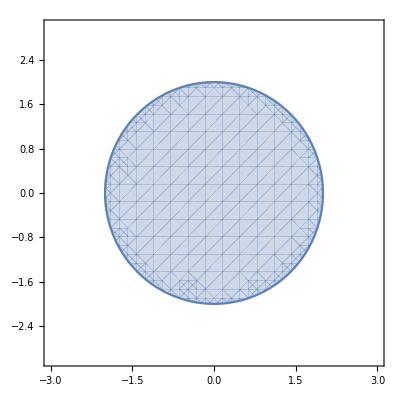

```mathematica
RegionPlot[d /. transform1, {r, range1[[2]], range1[[3]]}, {θ, range2[[2]], range2[[3]]}]
RegionPlot[d, {x, range3[[2]], range3[[3]]}, {y, range4[[2]], range4[[3]]}]
```

```mathematica
transform2[v_] := {v[[1]] Cos[v[[2]]], v[[1]] Sin[v[[2]]]};
paths = Flatten[Table[{{r, 2π*t}, {4t, θ}}, {r, 0, 4, 1}, {θ, 0, 2 π, π / 3}], 2];
tmin = 0;
tmax = 1;
xmin = -4;
xmax = 4;
ymin = -4;
ymax = 2 π;
duration = 6;
fps = 5;
```

```mathematica
frame[rt_]:= Show[ParametricPlot[#* rt  + transform2[#] * (1-rt), {t, tmin, tmax},PlotRange->{{xmin, xmax}, {ymin, ymax}}]&/@paths];
frames = Table[Image[frame[u]], {u, 0, 1, 1 / (fps * duration)}];
(*animation = ListAnimate[frames, fps]*)
```

$Aborted

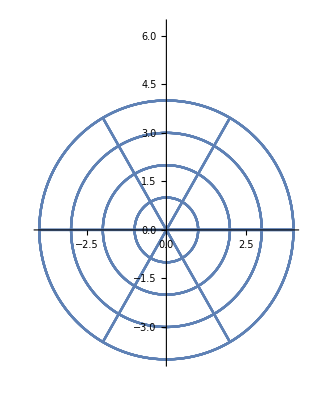

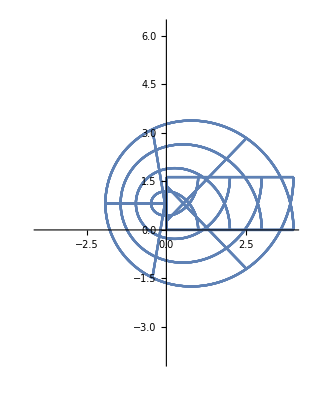

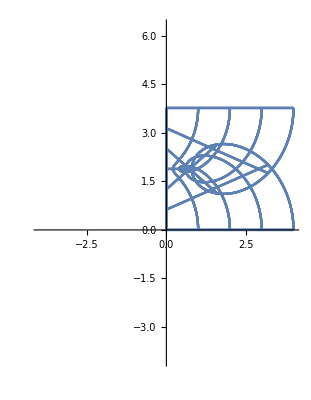

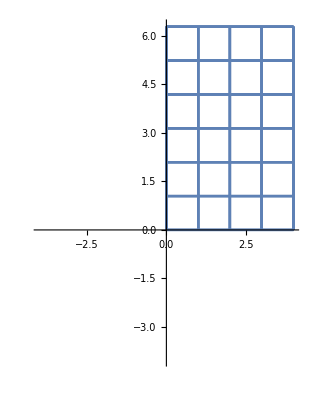

```mathematica
frame[0]
frame[0.26]
frame[0.60]
frame[1]
```

```mathematica
Export["change_of_variables.avi", animation]
```

change_of_variables.avi